```mathematica
(* How do you calculate the area of the intersection of an arbitrary triangle with a square? *)
𝒯=Triangle[{{a,b},{c,d},{e,f}}];
𝒮=Rectangle[{g,h},{i,j}];
```

```mathematica
ℐ=RegionIntersection[𝒯, 𝒮]
```

BooleanRegion[#1&&#2&,{Triangle[{{a,b},{c,d},{e,f}}],Rectangle[{g,h},{i,j}]}]

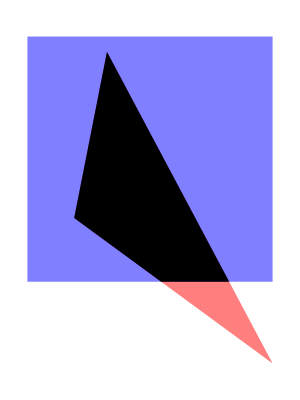

```mathematica
Graphics[{{Opacity[0.5],{Red, 𝒯},{Blue, 𝒮}}, ℐ}]/.{a->RandomReal[], b->RandomReal[], c->RandomReal[],d->RandomReal[],e->1,f-> 0,g-> 1/4,h-> 1/4,i-> 1,j-> 1}
```

```mathematica
Area[ℐ]
```

$Aborted

```mathematica
(* Try with a couple of implicit circles: *)
ℛ1=ImplicitRegion[(x-a1)^2+(y-b1)^2≤r1,{x,y}];
ℛ2=ImplicitRegion[(x-a2)^2+(y-b2)^2≤r2,{x,y}];
```

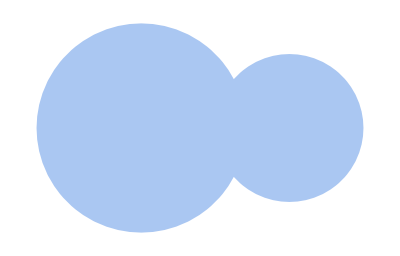

```mathematica
Show[Region[ℛ1],Region[ℛ2]]/.{a1->0,b1->0,r1->2,a2->2,b2->0,r2->1}
```

```mathematica
ℐ=RegionIntersection[ℛ1, ℛ2]
```

ImplicitRegion[(a1-x)^2+(b1-y)^2≤r1&&(a2-x)^2+(b2-y)^2≤r2,{x,y}]

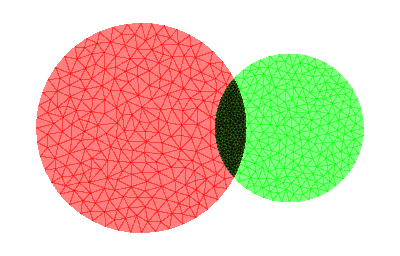

```mathematica
Graphics[{{Opacity[0.5],{Red,DiscretizeRegion[ℛ1]}, {Green,DiscretizeRegion[ℛ2]}, DiscretizeRegion[ℐ/.{a1->0,b1->0,r1->2,a2->2,b2->0,r2->1}]}}/.{a1->0,b1->0,r1->2,a2->2,b2->0,r2->1}]
```

```mathematica
ℰ=ℐ/.{a1->0,b1->0,r1->2,a2->2,b2->0,r2->1}//Evaluate
```

ImplicitRegion[x^2+y^2≤2&&(2-x)^2+y^2≤1,{x,y}]

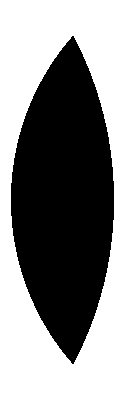

```mathematica
Graphics[DiscretizeRegion[ℰ]]
```

```mathematica
𝒟=DiscretizeRegion[ℐ]
```

$Aborted